```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
ClearAll[fs]
fs = Style[#, FontSize-> 16]&;
```

/Users/pjoot/project/figures/phy456-qmII

```mathematica
Manipulate[
Plot[
Sinc[ω t - Subscript[ω, 0]] + Sinc[ω t+Subscript[ω, 0]], 
{t, -r, r}, 
PlotRange->{-0.3,1.2},
PlotStyle-> Thick,
Ticks -> None
],{{r, 30},5,40}, {{Subscript[ω, 0], 28}, 1, 50}, {{ω, 2}, 1, 10}] (* /. {Subscript[ω, 0] -> 28, ω -> 2} *)
```

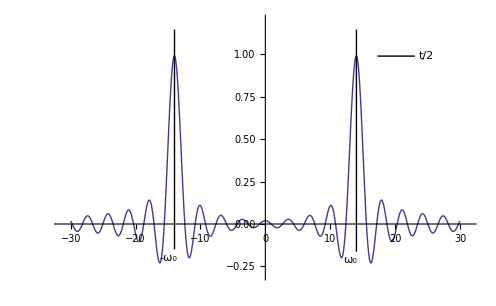

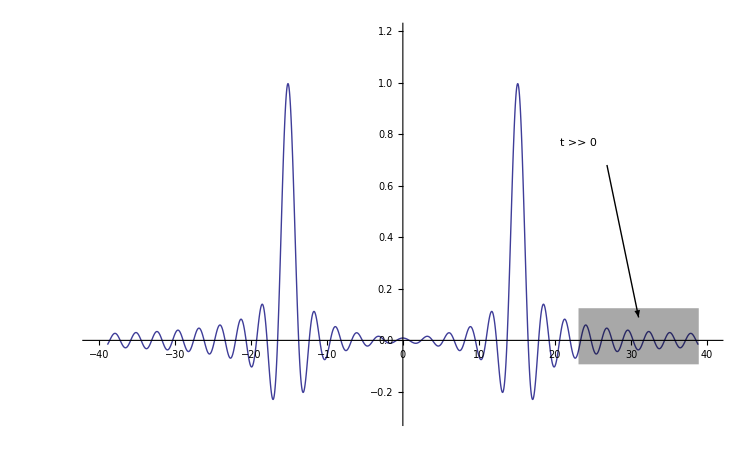

```mathematica
ClearAll[p, f]
f[w_, t_,w0_] := Sinc[(w - w0)t/2]+ Sinc[(w + w0)t/2]
(*p = With[{r = 30,ω0= 28,t = 2 },
Plot[
{
Callout[f[ω ,t, ω0], "(-ω_0, A_mi/ℏ)"//fs,{ -ω0, t/2}],
Callout[f[ω ,t, ω0], "(ω_0, A_mi/ℏ )"//fs,{ ω0, t/2}],
f[ω ,t, ω0]
}
, {ω, -2 ω0, 2 ω0}
, PlotRange->{{-2 ω0, 2 ω0 },{-.2t,.7t}}
,PlotStyle-> Thick
,Ticks -> None
]
];*)
g[w_, t_] := t/2
p = With[{r = 30,ω0= 28,t = 2 },
p1 = Plot[
{
Callout[g[ω, t], " A_mi/ℏ"//fs,{1.7 ω0, t/2}],
g[ω, t]
}
, {ω, -2 ω0, 2 ω0}
, PlotRange->{{-2 ω0, 2 ω0 },{-.2t,.7t}}
,PlotStyle-> Thick
,Ticks -> None
];
p2 = Plot[
{
Callout[f[ω ,t, ω0], "-ω_0" //fs,{ -ω0, t/2}],
Callout[f[ω ,t, ω0], "ω_0"//fs,{ ω0, t/2}],
f[ω ,t, ω0]
}
, {ω, -2 ω0, 2 ω0}
, PlotRange->{{-2 ω0, 2 ω0 },{-.2t,.7t}}
,PlotStyle-> Thick
,Ticks -> None
];
Show[{p1,p2}]
]
```

-Graphics-

```mathematica
peeters`exportForLatex["qmTwoL10fig3", p]
```

{qmTwoL10fig3.eps,qmTwoL10fig3pn.png}